## Orthogonal Matrices

```mathematica
RandomOrthAugment[Q_,s_Integer]:=Module[{m,n,S},
{m,n}=Dimensions[Q];
S=RandomReal[{-1,1},{m,s}];
S-=Q.Qᵀ.S;
QRDecomposition[S]⟦1⟧ᵀ]

RandomOrth[{m_,n_}]:=Module[{S},
S=RandomReal[{-1,1},{m,n}];
QRDecomposition[S]⟦1⟧ᵀ]
```

Testing

```mathematica
{m,n,s}={12,3,4};
Q=RandomOrth[{m,n}];
AugQ=RandomOrthAugment[Q,s];
BigQ=ArrayFlatten[{{Q,AugQ}}];
{Dimensions[Q]=={m,n},Dimensions[NewQ]=={m,s},
OrthogonalMatrixQ[Q],
OrthogonalMatrixQ[BigQ]}
```

{True,True,True,True}

## Making Low Rank Matrices

```mathematica
LowRankBuild[{m_,n_},σs_]:= Module[{U,V,r=Length[σs]},
{U,V}=Map[RandomOrth[{#,r}]&, {m,n}];
U.DiagonalMatrix[σs].Vᵀ]
```

Testing

```mathematica
{m,n}={123,56};
σs=Sort[{1,2,3,4,5,6,7,8,9.3}];
A=LowRankBuild[{m,n},σs];
{Dimensions[A]=={m,n}, Norm[σs-Sort[SingularValueList[A]]]}
```

{True,4.08224×10^-15}

## Basic Algorithm: Initialization

I need to initialize the algorithm with a “consistent” low rank approximation.

```mathematica
LowRankInit[A_,s_]:= Module[{m,n,SL,SR,TwoSidedSample,
σ, Tol=10^-15,U,S,V},
{m,n}= Dimensions[A];
{SL,SR}=Map[RandomOrth[{#,s}]&,{m,n}];
TwoSidedSample=SLᵀ.A.SR;
σ=SingularValueList[TwoSidedSample, Tolerance->Tol];
{U,S,V}=SingularValueDecomposition[TwoSidedSample,Length[σ]];
{SL.U,Diagonal[S],SR.V}
]
```

Testing.  If the

```mathematica
{m,n}={123,56};
σs=Sort[{1,2,3,4,5,6,7,8,9.3}];
A=LowRankBuild[{m,n},σs];
s=12;
{U,σ,V}=LowRankInit[A,s];
{OrthogonalMatrixQ[U],OrthogonalMatrixQ[V],Length[σ],
Norm[Uᵀ.A.V-DiagonalMatrix[σ]]}
```

{True,True,9,1.74387×10^-15}

## Low Rank Iterate

The iteration is pretty easy.

```mathematica
LowRankUpDate[A_,{U_,σ_,V_}, {sL_,sR_}]:= Module[
{m,n,UA,VA,ReSample,UIn,σIn,VIn},
{m,n}=Dimensions[A];
{UA,VA}= MapThread[RandomOrthAugment,{{U,V},{sL,sR}}];
ReSample=ArrayFlatten[({{DiagonalMatrix[σ], Uᵀ.A.VA}, {UAᵀ.A.V, UAᵀ.A.VA}})];
{UIn,σIn,VIn}=SingularValueDecomposition[NewSample];
{ArrayFlatten[{{U,UA}}].UIn,Diagonal[σIn],ArrayFlatten[{{V,VA}}].VIn}
]
```

Testing

```mathematica
{m,n}={123,56};
σs=Sort[{1,2,3,4,5,6,7,8,9.3}];
A=LowRankBuild[{m,n},σs];
s=12;
{U,σ,V}=LowRankInit[A,s];
{sL,sR}={2,3};
{UNew,σNew,VNew}=LowRankUpDate[A,{U,σ,V},{sL,sR}];
{σ,σNew}
```

{{1.28477,1.06795,0.685656,0.602133,0.444469,0.314018,0.137042,0.130799,0.0261485},{1.81427,1.66647,1.51251,0.712213,0.549856,0.358951,0.185381,0.130917,0.0819322,0.,0.}}

```mathematica
σ
```

{1.38788,1.17765,1.02837,0.673358,0.487247,0.413869,0.120236,0.0759376,0.0611149,0.,0.,0.}

```mathematica
?MapThread
```

The basic algorithm

```mathematica
LowRankBuild[{m_,n_},σs_]:= Module[{U,V,r=Length[σs]},
{U,V}=Map[RandomOrth[{#,r}]&, {m,n}];
U.DiagonalMatrix[σs].Vᵀ]
```

Testing

```mathematica
{m,n}={123,56};
σs=Sort[{1,2,3,4,5,6,7,8,9.3}];
A=LowRankBuild[{m,n},σs];
{Dimensions[A]=={m,n}, Norm[σs-Sort[SingularValueList[A]]]}
```

{True,4.08224×10^-15}

## Break

128

{0.0441534,0.0459511,0.0591658,0.0827984,0.102966,0.103,0.120759,0.127166,0.134608,0.141043,0.151044,0.169141,0.179217,0.179564,0.184007,0.189359,0.194769,0.211003,0.214502,0.21643,0.221718,0.241492,0.26547,0.28278,0.294122,0.296109,0.310602,0.352189,0.422031,0.425853,0.429662,0.432919,0.450784,0.462414,0.473523,0.494871,0.501982,0.516446,0.538485,0.54463,0.554693,0.556388,0.561359,0.579872,0.595217,0.609842,0.640043,0.663755,0.670967,0.682388,0.684944,0.685242,0.699505,0.70112,0.722848,0.745205,0.7641,0.791492,0.79653,0.81102,0.83968,0.840466,0.841058,0.879197,0.884949,0.906415,0.962417,0.976327,1.02176,1.02449,1.03788,1.04634,1.06,1.07071,1.07079,1.07198,1.0802,1.08634,1.0903,1.11175,1.11265,1.18321,1.19744,1.21945,1.22188,1.26746,1.3404,1.36073,1.36264,1.37123,1.37358,1.39744,1.41807,1.4205,1.46233,1.48192,1.49825,1.51109,1.54719,1.56077,1.57429,1.60027,1.61565,1.62532,1.62873,1.63886,1.66949,1.78349,1.7996,1.84665,1.84847,1.91775,1.95907,1.99183,2.05222,2.15041,2.22095,2.26638,2.29669,2.42251,2.47223,2.51219,2.65635,2.66092,2.66109,2.70037,2.89261,3.75441}

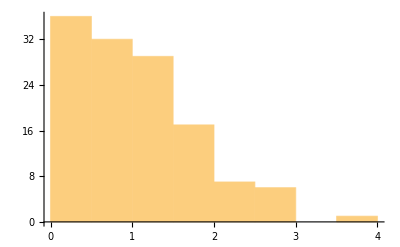

```mathematica
r=2^7
Hmm=Sort[RandomVariate[HalfNormalDistribution[1],r]]
Histogram[Hmm]
```

```mathematica
?HalfNormalDistribution
```